进行相关性检验，变量之间存在较强相关性才能使用PCA

```mathematica
data=;
```

```mathematica
loan=Dataset[
AssociationThread[{"Income","Education","Age","Residence","Employ","Savings","Debt","CreditCard"}->#]&/@data]
```

统一量纲，将数据进行标准化处理/Standardize

```mathematica
(pc=PrincipalComponents[data,Method->"Correlation"])//MatrixForm
```

(1.33335 | 1.39825 | 0.166745 | 0.33201 | 0.152827 | 0.192567 | 0.231696 | 0.0252322
-1.76062 | -0.301583 | 1.48355 | -0.611358 | 0.463687 | 0.133411 | 0.236271 | -0.140491
-1.23167 | 1.41937 | 0.329183 | 0.0559856 | 0.383589 | -0.141085 | -0.406109 | -0.106638
-0.587205 | 1.20578 | 3.11918 | -0.0585712 | 0.142006 | -0.562173 | -0.172086 | 0.164451
-3.03459 | 1.72996 | 0.648297 | 0.923532 | -0.0137672 | 0.684479 | -0.0537051 | 0.254015
-2.22029 | -4.49923 | 0.0453349 | 0.82885 | 1.45979 | -0.422196 | 0.0643213 | -0.122484
1.44497 | -1.56344 | 0.518066 | -0.870899 | -0.101121 | -0.146138 | 0.366416 | -0.0148811
-0.183222 | -0.90985 | -0.908912 | 0.0944347 | -1.50009 | -0.263571 | 0.54894 | -0.0281543
-0.898392 | 0.664677 | -1.089 | -0.505966 | 0.369236 | 0.301911 | 0.298509 | -0.029951
0.802604 | 1.91711 | -1.34419 | 0.0509839 | 0.563918 | 0.218075 | -0.366021 | -0.0267384
1.73861 | 0.668673 | -0.467 | 0.313895 | 0.838519 | -0.386344 | 0.276019 | 0.584307
2.92229 | -1.10973 | -0.917265 | 0.330042 | 0.389019 | 0.390977 | 0.0263019 | -0.0868535
-0.705366 | -2.58772 | 0.594488 | -0.0608865 | -1.17896 | 0.0830585 | -0.428684 | 0.0806223
1.73482 | -2.07722 | 1.161 | -1.16135 | 0.102084 | 0.151564 | -0.10237 | -0.0565725
-2.42351 | 0.279587 | -1.58797 | -0.76393 | 0.119649 | 0.0631217 | 0.321193 | 0.241517
-3.21629 | -0.769979 | 0.727788 | 1.17918 | 0.215462 | 0.768598 | 0.579876 | -0.0823559
-1.47486 | 1.0059 | -0.52931 | -0.259235 | 0.58851 | -0.964182 | -0.682001 | -0.0772977
-3.60503 | -0.227433 | -1.87658 | -1.81131 | -0.0644245 | 0.0537992 | -0.279111 | -0.0604482
2.86102 | -1.80624 | 0.133246 | -0.55423 | -0.0681177 | 0.494032 | -0.381311 | 0.348339
1.23533 | 1.42174 | 0.521219 | 0.640702 | -0.0358246 | 0.0261329 | -0.0652639 | -0.205096
1.71943 | 0.413252 | -0.127321 | -0.0687494 | -0.582396 | -0.0696252 | 0.0928483 | -0.133478
0.0316277 | 1.33402 | -0.179212 | -0.025764 | 0.0540795 | 0.509973 | -0.0818391 | -0.32524
1.53177 | 0.967987 | 0.236778 | -0.463721 | 0.0983247 | 0.0665587 | 0.362614 | -0.069118
-1.85401 | -0.168607 | -0.377343 | 0.914489 | -1.11199 | -0.281873 | -0.204799 | 0.429206
-0.417319 | 0.572357 | 1.28335 | -0.58029 | -0.700178 | 0.467771 | -0.537478 | -0.0838858
2.46414 | -0.988289 | -1.03645 | 1.31894 | 0.600456 | 0.239754 | -0.606292 | -0.0494855
1.95439 | 0.988005 | 0.120953 | -0.499803 | 0.163029 | -0.120104 | 0.469626 | 0.125593
1.52747 | 0.769571 | 0.287865 | -0.23708 | 0.0425449 | -0.419478 | 0.198616 | -0.0849881
0.886733 | -0.155727 | -0.864538 | 1.01719 | -1.22778 | -0.347227 | -0.0917934 | -0.222415
-0.576175 | 0.408809 | -0.071957 | 0.532907 | -0.162076 | -0.721786 | 0.385615 | -0.246712)

```mathematica
pc//Dimensions
```

{30,8}

```mathematica
(ev=Eigenvectors[Correlation[data]])//MatrixForm
```

(-0.313901 | -0.236961 | -0.48396 | -0.466392 | -0.458923 | -0.404067 | 0.0672231 | 0.123192
0.144645 | 0.444102 | -0.135096 | -0.276586 | -0.304457 | 0.21894 | -0.585055 | -0.451866
0.67586 | 0.400867 | 0.0041369 | -0.0906608 | -0.12175 | -0.366485 | 0.0780092 | 0.468042
-0.346949 | 0.239837 | -0.211519 | 0.115722 | -0.0170589 | 0.435753 | -0.280962 | 0.703464
0.241341 | -0.622183 | 0.174953 | 0.0352873 | 0.0143773 | -0.143142 | -0.68126 | 0.194877
-0.493878 | 0.35695 | 0.48733 | 0.0851997 | 0.0230804 | -0.568094 | -0.245331 | 0.0217116
0.0177428 | 0.103082 | -0.657255 | 0.487289 | 0.367866 | -0.34797 | -0.195687 | -0.157869
-0.030123 | 0.0570635 | -0.0518793 | -0.662127 | 0.738591 | -0.0173144 | -0.0746357 | 0.0578374)

```mathematica
TableForm[Transpose@ev,TableHeadings->{{"Income","Education","Age","Residence","Employ","Savings","Debt","CreditCard"},
Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
Income | -0.313901 | 0.144645 | 0.67586 | -0.346949 | 0.241341 | -0.493878 | 0.0177428 | -0.030123
Education | -0.236961 | 0.444102 | 0.400867 | 0.239837 | -0.622183 | 0.35695 | 0.103082 | 0.0570635
Age | -0.48396 | -0.135096 | 0.0041369 | -0.211519 | 0.174953 | 0.48733 | -0.657255 | -0.0518793
Residence | -0.466392 | -0.276586 | -0.0906608 | 0.115722 | 0.0352873 | 0.0851997 | 0.487289 | -0.662127
Employ | -0.458923 | -0.304457 | -0.12175 | -0.0170589 | 0.0143773 | 0.0230804 | 0.367866 | 0.738591
Savings | -0.404067 | 0.21894 | -0.366485 | 0.435753 | -0.143142 | -0.568094 | -0.34797 | -0.0173144
Debt | 0.0672231 | -0.585055 | 0.0780092 | -0.280962 | -0.68126 | -0.245331 | -0.195687 | -0.0746357
CreditCard | 0.123192 | -0.451866 | 0.468042 | 0.703464 | 0.194877 | 0.0217116 | -0.157869 | 0.0578374

```mathematica
Standardize[data].Transpose[Eigenvectors[Correlation[data]]]//MatrixForm
```

(1.33335 | 1.39825 | 0.166745 | -0.33201 | -0.152827 | -0.192567 | 0.231696 | 0.0252322
-1.76062 | -0.301583 | 1.48355 | 0.611358 | -0.463687 | -0.133411 | 0.236271 | -0.140491
-1.23167 | 1.41937 | 0.329183 | -0.0559856 | -0.383589 | 0.141085 | -0.406109 | -0.106638
-0.587205 | 1.20578 | 3.11918 | 0.0585712 | -0.142006 | 0.562173 | -0.172086 | 0.164451
-3.03459 | 1.72996 | 0.648297 | -0.923532 | 0.0137672 | -0.684479 | -0.0537051 | 0.254015
-2.22029 | -4.49923 | 0.0453349 | -0.82885 | -1.45979 | 0.422196 | 0.0643213 | -0.122484
1.44497 | -1.56344 | 0.518066 | 0.870899 | 0.101121 | 0.146138 | 0.366416 | -0.0148811
-0.183222 | -0.90985 | -0.908912 | -0.0944347 | 1.50009 | 0.263571 | 0.54894 | -0.0281543
-0.898392 | 0.664677 | -1.089 | 0.505966 | -0.369236 | -0.301911 | 0.298509 | -0.029951
0.802604 | 1.91711 | -1.34419 | -0.0509839 | -0.563918 | -0.218075 | -0.366021 | -0.0267384
1.73861 | 0.668673 | -0.467 | -0.313895 | -0.838519 | 0.386344 | 0.276019 | 0.584307
2.92229 | -1.10973 | -0.917265 | -0.330042 | -0.389019 | -0.390977 | 0.0263019 | -0.0868535
-0.705366 | -2.58772 | 0.594488 | 0.0608865 | 1.17896 | -0.0830585 | -0.428684 | 0.0806223
1.73482 | -2.07722 | 1.161 | 1.16135 | -0.102084 | -0.151564 | -0.10237 | -0.0565725
-2.42351 | 0.279587 | -1.58797 | 0.76393 | -0.119649 | -0.0631217 | 0.321193 | 0.241517
-3.21629 | -0.769979 | 0.727788 | -1.17918 | -0.215462 | -0.768598 | 0.579876 | -0.0823559
-1.47486 | 1.0059 | -0.52931 | 0.259235 | -0.58851 | 0.964182 | -0.682001 | -0.0772977
-3.60503 | -0.227433 | -1.87658 | 1.81131 | 0.0644245 | -0.0537992 | -0.279111 | -0.0604482
2.86102 | -1.80624 | 0.133246 | 0.55423 | 0.0681177 | -0.494032 | -0.381311 | 0.348339
1.23533 | 1.42174 | 0.521219 | -0.640702 | 0.0358246 | -0.0261329 | -0.0652639 | -0.205096
1.71943 | 0.413252 | -0.127321 | 0.0687494 | 0.582396 | 0.0696252 | 0.0928483 | -0.133478
0.0316277 | 1.33402 | -0.179212 | 0.025764 | -0.0540795 | -0.509973 | -0.0818391 | -0.32524
1.53177 | 0.967987 | 0.236778 | 0.463721 | -0.0983247 | -0.0665587 | 0.362614 | -0.069118
-1.85401 | -0.168607 | -0.377343 | -0.914489 | 1.11199 | 0.281873 | -0.204799 | 0.429206
-0.417319 | 0.572357 | 1.28335 | 0.58029 | 0.700178 | -0.467771 | -0.537478 | -0.0838858
2.46414 | -0.988289 | -1.03645 | -1.31894 | -0.600456 | -0.239754 | -0.606292 | -0.0494855
1.95439 | 0.988005 | 0.120953 | 0.499803 | -0.163029 | 0.120104 | 0.469626 | 0.125593
1.52747 | 0.769571 | 0.287865 | 0.23708 | -0.0425449 | 0.419478 | 0.198616 | -0.0849881
0.886733 | -0.155727 | -0.864538 | -1.01719 | 1.22778 | 0.347227 | -0.0917934 | -0.222415
-0.576175 | 0.408809 | -0.071957 | -0.532907 | 0.162076 | 0.721786 | 0.385615 | -0.246712)

```mathematica
var=Variance[pc]
```

{3.54757,2.13199,1.04474,0.531512,0.411203,0.166488,0.125356,0.0411433}

```mathematica
Chop@Covariance[pc]//MatrixForm
```

(3.54757 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.13199 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.04474 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.531512 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.411203 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.166488 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.125356 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0411433)

```mathematica
Normalize[var,Total]
```

{0.443446,0.266499,0.130592,0.066439,0.0514003,0.020811,0.0156695,0.00514292}

```mathematica
Accumulate[%]
```

{0.443446,0.709945,0.840537,0.906976,0.958377,0.979188,0.994857,1.}

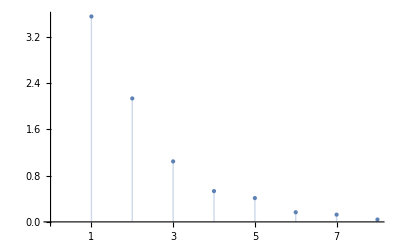

```mathematica
ListPlot[var,PlotStyle->PointSize[Large],Ticks-> {{1,2,3,4,5,6,7,8},Automatic},Mesh->All,Filling->Bottom]
```

分值图

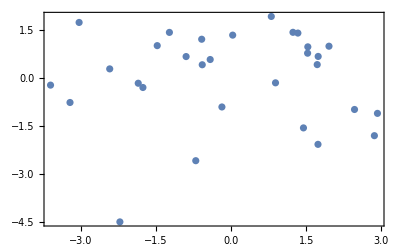

```mathematica
scorePlot=ListPlot[pc[[All,{1,2}]],Frame->True,PlotRange->All]
```

```mathematica
kld=KarhunenLoeveDecomposition[Transpose[Standardize@data]]
```

{{{1.33335,-1.76062,-1.23167,-0.587205,-3.03459,-2.22029,1.44497,-0.183222,-0.898392,0.802604,1.73861,2.92229,-0.705366,1.73482,-2.42351,-3.21629,-1.47486,-3.60503,2.86102,1.23533,1.71943,0.0316277,1.53177,-1.85401,-0.417319,2.46414,1.95439,1.52747,0.886733,-0.576175},{1.39825,-0.301583,1.41937,1.20578,1.72996,-4.49923,-1.56344,-0.90985,0.664677,1.91711,0.668673,-1.10973,-2.58772,-2.07722,0.279587,-0.769979,1.0059,-0.227433,-1.80624,1.42174,0.413252,1.33402,0.967987,-0.168607,0.572357,-0.988289,0.988005,0.769571,-0.155727,0.408809},{0.166745,1.48355,0.329183,3.11918,0.648297,0.0453349,0.518066,-0.908912,-1.089,-1.34419,-0.467,-0.917265,0.594488,1.161,-1.58797,0.727788,-0.52931,-1.87658,0.133246,0.521219,-0.127321,-0.179212,0.236778,-0.377343,1.28335,-1.03645,0.120953,0.287865,-0.864538,-0.071957},{0.33201,-0.611358,0.0559856,-0.0585712,0.923532,0.82885,-0.870899,0.0944347,-0.505966,0.0509839,0.313895,0.330042,-0.0608865,-1.16135,-0.76393,1.17918,-0.259235,-1.81131,-0.55423,0.640702,-0.0687494,-0.025764,-0.463721,0.914489,-0.58029,1.31894,-0.499803,-0.23708,1.01719,0.532907},{0.152827,0.463687,0.383589,0.142006,-0.0137672,1.45979,-0.101121,-1.50009,0.369236,0.563918,0.838519,0.389019,-1.17896,0.102084,0.119649,0.215462,0.58851,-0.0644245,-0.0681177,-0.0358246,-0.582396,0.0540795,0.0983247,-1.11199,-0.700178,0.600456,0.163029,0.0425449,-1.22778,-0.162076},{0.192567,0.133411,-0.141085,-0.562173,0.684479,-0.422196,-0.146138,-0.263571,0.301911,0.218075,-0.386344,0.390977,0.0830585,0.151564,0.0631217,0.768598,-0.964182,0.0537992,0.494032,0.0261329,-0.0696252,0.509973,0.0665587,-0.281873,0.467771,0.239754,-0.120104,-0.419478,-0.347227,-0.721786},{0.231696,0.236271,-0.406109,-0.172086,-0.0537051,0.0643213,0.366416,0.54894,0.298509,-0.366021,0.276019,0.0263019,-0.428684,-0.10237,0.321193,0.579876,-0.682001,-0.279111,-0.381311,-0.0652639,0.0928483,-0.0818391,0.362614,-0.204799,-0.537478,-0.606292,0.469626,0.198616,-0.0917934,0.385615},{0.0252322,-0.140491,-0.106638,0.164451,0.254015,-0.122484,-0.0148811,-0.0281543,-0.029951,-0.0267384,0.584307,-0.0868535,0.0806223,-0.0565725,0.241517,-0.0823559,-0.0772977,-0.0604482,0.348339,-0.205096,-0.133478,-0.32524,-0.069118,0.429206,-0.0838858,-0.0494855,0.125593,-0.0849881,-0.222415,-0.246712}},{{-0.313901,-0.236961,-0.48396,-0.466392,-0.458923,-0.404067,0.0672231,0.123192},{0.144645,0.444102,-0.135096,-0.276586,-0.304457,0.21894,-0.585055,-0.451866},{0.67586,0.400867,0.0041369,-0.0906608,-0.12175,-0.366485,0.0780092,0.468042},{0.346949,-0.239837,0.211519,-0.115722,0.0170589,-0.435753,0.280962,-0.703464},{-0.241341,0.622183,-0.174953,-0.0352873,-0.0143773,0.143142,0.68126,-0.194877},{0.493878,-0.35695,-0.48733,-0.0851997,-0.0230804,0.568094,0.245331,-0.0217116},{0.0177428,0.103082,-0.657255,0.487289,0.367866,-0.34797,-0.195687,-0.157869},{-0.030123,0.0570635,-0.0518793,-0.662127,0.738591,-0.0173144,-0.0746357,0.0578374}}}

```mathematica
var
```

{3.54757,2.13199,1.04474,0.531512,0.411203,0.166488,0.125356,0.0411433}

```mathematica
Covariance[Transpose[kld[[1]]]]//Chop//MatrixForm
```

(3.54757 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.13199 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.04474 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.531512 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.411203 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.166488 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.125356 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0411433)

```mathematica
-kld[[2]]//Transpose//MatrixForm
```

(0.313901 | -0.144645 | -0.67586 | -0.346949 | 0.241341 | -0.493878 | -0.0177428 | 0.030123
0.236961 | -0.444102 | -0.400867 | 0.239837 | -0.622183 | 0.35695 | -0.103082 | -0.0570635
0.48396 | 0.135096 | -0.0041369 | -0.211519 | 0.174953 | 0.48733 | 0.657255 | 0.0518793
0.466392 | 0.276586 | 0.0906608 | 0.115722 | 0.0352873 | 0.0851997 | -0.487289 | 0.662127
0.458923 | 0.304457 | 0.12175 | -0.0170589 | 0.0143773 | 0.0230804 | -0.367866 | -0.738591
0.404067 | -0.21894 | 0.366485 | 0.435753 | -0.143142 | -0.568094 | 0.34797 | 0.0173144
-0.0672231 | 0.585055 | -0.0780092 | -0.280962 | -0.68126 | -0.245331 | 0.195687 | 0.0746357
-0.123192 | 0.451866 | -0.468042 | 0.703464 | 0.194877 | 0.0217116 | 0.157869 | -0.0578374)

```mathematica
-kld[[2,1]]
```

{0.313901,0.236961,0.48396,0.466392,0.458923,0.404067,-0.0672231,-0.123192}

载荷图

```mathematica
loadingPlot=With[{pts=kld[[2,{1,2}]]//Transpose},
ListPlot[
MapThread[Callout[#1,#2]&,{pts,{"Income","Education","Age","Address","Service","Savings","Debt","CreditCard"}}],
Prolog->{ Line[{{0,0},#}]&/@pts}]
]
```

-Graphics-

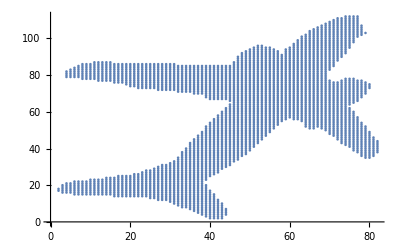

```mathematica
ListPlot[shape]
```

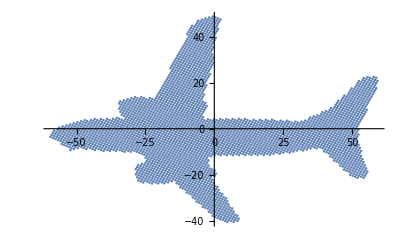

```mathematica
ListPlot[PrincipalComponents[shape]]
```

```mathematica
MahalanobisDistanceSq[data_,mu_]:=With[{inv=Inverse@Covariance[data],m=Mean[data]},(m-mu).inv.(m-mu)]
```

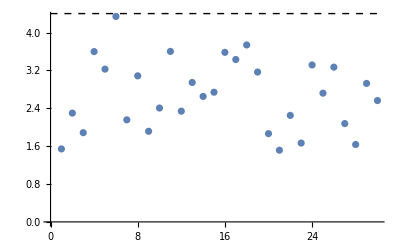

```mathematica
ListPlot[√(MahalanobisDistanceSq[data,#]&/@(data)),Epilog->{Dashed,Line[{{0,4.4},{30,4.4}}]}]
```

```mathematica
kld[[2,All]]//Transpose//MatrixForm
```

(-0.313901 | 0.144645 | 0.67586 | 0.346949 | -0.241341 | 0.493878 | 0.0177428 | -0.030123
-0.236961 | 0.444102 | 0.400867 | -0.239837 | 0.622183 | -0.35695 | 0.103082 | 0.0570635
-0.48396 | -0.135096 | 0.0041369 | 0.211519 | -0.174953 | -0.48733 | -0.657255 | -0.0518793
-0.466392 | -0.276586 | -0.0906608 | -0.115722 | -0.0352873 | -0.0851997 | 0.487289 | -0.662127
-0.458923 | -0.304457 | -0.12175 | 0.0170589 | -0.0143773 | -0.0230804 | 0.367866 | 0.738591
-0.404067 | 0.21894 | -0.366485 | -0.435753 | 0.143142 | 0.568094 | -0.34797 | -0.0173144
0.0672231 | -0.585055 | 0.0780092 | 0.280962 | 0.68126 | 0.245331 | -0.195687 | -0.0746357
0.123192 | -0.451866 | 0.468042 | -0.703464 | -0.194877 | -0.0217116 | -0.157869 | 0.0578374)

通过内积来计算每个数据的分值

```mathematica
data2=ArrayFlatten[{{data,Abs[Standardize[data].(-kld[[2,;;3]]//Transpose)]}}]
```

{{50000.,16.,28.,2.,2.,5000.,1200.,2.,1.33335,1.39825,0.166745},{72000.,18.,35.,10.,8.,12000.,5400.,4.,1.76062,0.301583,1.48355},{61000.,18.,36.,6.,5.,15000.,1000.,2.,1.23167,1.41937,0.329183},{88000.,20.,35.,4.,4.,980.,1100.,4.,0.587205,1.20578,3.11918},{91100.,18.,38.,8.,9.,20000.,0.,1.,3.03459,1.72996,0.648297},{45100.,14.,41.,15.,14.,3900.,22000.,4.,2.22029,4.49923,0.0453349},{36200.,14.,29.,6.,5.,100.,7000.,5.,1.44497,1.56344,0.518066},{41000.,12.,34.,9.,8.,5000.,200.,3.,0.183222,0.90985,0.908912},{40000.,16.,32.,8.,7.,19000.,1760.,2.,0.898392,0.664677,1.089},{32000.,16.,30.,2.,2.,16000.,550.,1.,0.802604,1.91711,1.34419},{29000.,16.,28.,1.,4.,2100.,4600.,2.,1.73861,0.668673,0.467},{21240.,12.,26.,2.,2.,100.,10010.,3.,2.92229,1.10973,0.917265},{58700.,12.,38.,9.,9.,4500.,7800.,5.,0.705366,2.58772,0.594488},{41000.,14.,29.,5.,4.,300.,10000.,6.,1.73482,2.07722,1.161},{38720.,16.,36.,11.,11.,24500.,540.,2.,2.42351,0.279587,1.58797},{88240.,16.,38.,13.,12.,13600.,8100.,2.,3.21629,0.769979,0.727788},{40000.,18.,39.,7.,6.,16000.,1300.,2.,1.47486,1.0059,0.52931},{34600.,16.,40.,14.,12.,34000.,100.,3.,3.60503,0.227433,1.87658},{29800.,12.,27.,1.,3.,100.,10000.,5.,2.86102,1.80624,0.133246},{56400.,16.,30.,2.,1.,3000.,1200.,2.,1.23533,1.42174,0.521219},{39800.,14.,29.,3.,2.,2500.,900.,3.,1.71943,0.413252,0.127321},{54200.,16.,31.,5.,3.,14200.,800.,2.,0.0316277,1.33402,0.179212},{42650.,16.,27.,3.,2.,5200.,1000.,3.,1.53177,0.967987,0.236778},{62200.,14.,40.,8.,10.,10000.,700.,2.,1.85401,0.168607,0.377343},{72200.,16.,34.,5.,4.,12000.,400.,4.,0.417319,0.572357,1.28335},{26530.,12.,30.,1.,2.,0.,12000.,2.,2.46414,0.988289,1.03645},{36500.,16.,26.,2.,2.,3100.,800.,3.,1.95439,0.988005,0.120953},{40000.,16.,29.,3.,2.,1900.,1300.,3.,1.52747,0.769571,0.287865},{41200.,12.,34.,5.,4.,1000.,1200.,2.,0.886733,0.155727,0.864538},{50000.,16.,35.,8.,6.,4500.,1400.,2.,0.576175,0.408809,0.071957}}

```mathematica
ds=Dataset[
AssociationThread[{"Income","Education","Age","Residence","Employ","Savings","Debt","CreditCard","pc1","pc2","pc3"}->#]&/@data2]
```

```mathematica
SortBy[ds,"pc2"]
```

从 PCA 还原 eigenvector

```mathematica
solver=LinearSolve[Standardize[data][[;;8]]]
```

LinearSolveFunction[…]

```mathematica
eigV=Table[solver[pc[[;;8,k]]],{k,1,8}]
```

{{-0.313901,-0.236961,-0.48396,-0.466392,-0.458923,-0.404067,0.0672231,0.123192},{0.144645,0.444102,-0.135096,-0.276586,-0.304457,0.21894,-0.585055,-0.451866},{0.67586,0.400867,0.0041369,-0.0906608,-0.12175,-0.366485,0.0780092,0.468042},{0.346949,-0.239837,0.211519,-0.115722,0.0170589,-0.435753,0.280962,-0.703464},{-0.241341,0.622183,-0.174953,-0.0352873,-0.0143773,0.143142,0.68126,-0.194877},{0.493878,-0.35695,-0.48733,-0.0851997,-0.0230804,0.568094,0.245331,-0.0217116},{0.0177428,0.103082,-0.657255,0.487289,0.367866,-0.34797,-0.195687,-0.157869},{-0.030123,0.0570635,-0.0518793,-0.662127,0.738591,-0.0173144,-0.0746357,0.0578374}}

```mathematica
-eigV//Transpose//MatrixForm
```

(0.313901 | -0.144645 | -0.67586 | -0.346949 | 0.241341 | -0.493878 | -0.0177428 | 0.030123
0.236961 | -0.444102 | -0.400867 | 0.239837 | -0.622183 | 0.35695 | -0.103082 | -0.0570635
0.48396 | 0.135096 | -0.0041369 | -0.211519 | 0.174953 | 0.48733 | 0.657255 | 0.0518793
0.466392 | 0.276586 | 0.0906608 | 0.115722 | 0.0352873 | 0.0851997 | -0.487289 | 0.662127
0.458923 | 0.304457 | 0.12175 | -0.0170589 | 0.0143773 | 0.0230804 | -0.367866 | -0.738591
0.404067 | -0.21894 | 0.366485 | 0.435753 | -0.143142 | -0.568094 | 0.34797 | 0.0173144
-0.0672231 | 0.585055 | -0.0780092 | -0.280962 | -0.68126 | -0.245331 | 0.195687 | 0.0746357
-0.123192 | 0.451866 | -0.468042 | 0.703464 | 0.194877 | 0.0217116 | 0.157869 | -0.0578374)